```mathematica
{k1,k2} = {10,10};
```

```mathematica
theta = 1;
```

```mathematica
{{xi11, xi12},{xi21, xi22}} = {{0,0},{0,0}};
```

```mathematica
{{eta11, eta12},{eta21, eta22}} = {{0,0},{0,0}};
```

```mathematica
{{zeta11, zeta12},{zeta21, zeta22}} = {{0,0},{0,1}};
```

```mathematica
{u0,v0} = {10,10};
```

```mathematica
proc = ItoProcess[{{k1 (u - v),k2 (theta - u)},{{xi11 v + eta11 u + zeta11, xi12 v + eta12 u + zeta12},{xi21 v + eta21 u + zeta21, xi22 v + eta22 u + zeta22}}},{{v,u},{v0,u0}},{t,0}]
```

ItoProcess[{{10 (u[t]-v[t]),10 (1-u[t])},{{0,0},{0,1}},{v[t],u[t]}},{{v,u},{10,10}},{t,0}]

```mathematica
f = RandomFunction[proc,{0.,1000,0.01}]["PathFunction"]
```

Function[x,InterpolatingFunction[{{0., 1000.}}, <>][x],Listable]

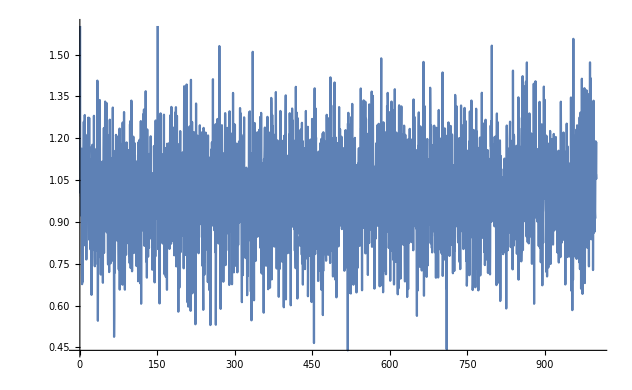

```mathematica
Plot[f[t][[1]],{t,0,1000}]
```

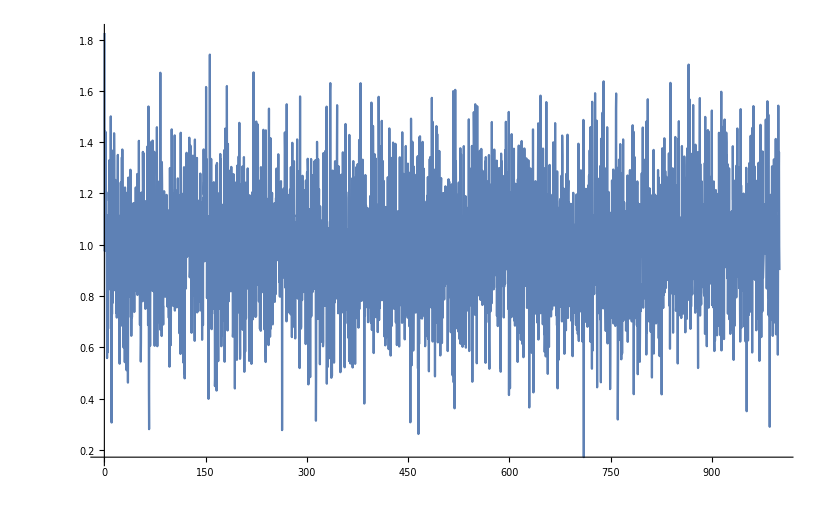

```mathematica
Plot[f[t][[2]],{t,0,1000}]
```